```mathematica
qi[k_]:=(q^k-q^-k)/(q-q^-1)
```

```mathematica
ν[m_][i_][T[i_,j_]]:=(-1)^j qi[m]^-1(
If[j>0,(-1)^(m-i)qi[i+j]T[i+1,j-1],0]+
If[i+j>m/2,(-1)^(m/2)qi[2i+j-m/2]T[i+1,j-2],0]+
If[i+j<m/2,(-1)^(m/2)qi[j+m/2]T[i+1,j],0]
)
```

```mathematica
ν[m_][i_][a_ t_T]:=a ν[m][i][t]
ν[m_][i_][X_Plus]:=ν[m][i]/@X
```

```mathematica
μ[m_][i_][T[i_,j_]]:=(-1)^i qi[m]^-1(qi[m-i]T[i,j+1]+(-1)^m qi[i]T[i,j-1])
```

```mathematica
μ[m_][i_][a_ t_T]:=a μ[m][i][t]
μ[m_][i_][X_Plus]:=μ[m][i]/@X
μ[m_][i_][X_Times]:=μ[m][i][Expand[X]]
```

```mathematica
With[{m=10,i=2,r=2},
With[{v=Sum[ζ[m-2i]^(j r)T[i,j],{j,0,m-2i-1}]},
Collect[
μ[m][i][v]-((-1)^i qi[m]^-1(qi[m-i] ζ[m-2i]^-r+(-1)^m qi[i] ζ[m-2i]^r))v/.{T[i,m-2i]:>T[i,0],T[i,-1]:>T[i,m-2i-1],ζ[k_]:>Exp[2π ⅈ/k]},
_T,Together]
]
]
```

0

```mathematica
(* The minus sign in the exponent of the root here is correct; confusion reigns when switching from matrices to linear transformations... *)
resμ[m_][i_,z_][T[i_,j_]]:=Sum[
1/(m-2i)(Sum[ζ[m-2i]^(-ℓ(j-jp))((-1)^i qi[m-i]/qi[m] ζ[m-2i]^-ℓ+(-1)^(m-i)qi[i]/qi[m] ζ[m-2i]^ℓ-z)^-1,{ℓ,0,m-2i-1}])T[i,jp]
,{jp,0,m-2i-1}]
```

```mathematica
resμ[m_][i_,z_][a_ t_T]:=a resμ[m][i,z][t]
resμ[m_][i_,z_][X_Plus]:=resμ[m][i,z]/@X
resμ[m_][i_,z_][X_Times]:=resμ[m][i,z][Expand[X]]
```

```mathematica
With[{m=10,i=0,j=0},Collect[resμ[m][i,z][μ[m][i][T[i,j]]-z T[i,j]]/.ζ[k_]:>Exp[2π ⅈ/k],_T,FullSimplify]]
```

T[0,0]

```mathematica
With[{m=10,i=1,j=2},Collect[resμ[m][i,z][μ[m][i][T[i,j]]-z T[i,j]]/.ζ[k_]:>Exp[2π ⅈ/k],_T,Together]]
```

T[1,2]

```mathematica
Clear[X]
X[m_,ω_][0]:=Sum[ω^-j T[0,j],{j,0,m-1}]
X[m_,ω_][i_]:=X[m,ω][i]=Collect[-resμ[m][i,ω][ν[m][i-1][X[m,ω][i-1]]],_T,Together]
```

```mathematica
Clear[ζ]
```

```mathematica
ζ/:ζ[n_]^m_/;m≥n:=ζ[n]^Mod[m,n]
```

```mathematica
ζ/:ζ[8]^(n_?EvenQ):=ⅈ^(n/2)
ζ/:ζ[8]^(n_?OddQ):=ⅈ^((n-1)/2)ζ[8]
```

```mathematica
ζ/:ζ[6]^(n_/;n≥3):=ζ[6]^Mod[n,3](-1)^Floor[n/3]
```

```mathematica
γ[j_]/;j>1:=γ[Mod[j,2]]
```

```mathematica
Clear[a]
a[m_][σ_,ω_]:=a[m][σ,ω]=Collect[X[m,ω][1]/.T[1,j_]:>σ^j γ[j+1],_γ,Together]
```

```mathematica
Clear[b]
b[n_][σ_,ω_]:=b[n][σ,ω]=∑_(j=0)^n (ω^-j+ω^(-j+n+1))((-1)^j(σ^j qi[2n+2-j]+σ^(j-2)qi[j])γ[j]+(-1)^(n+j+1)(σ^(j+1)qi[n+1-j]+σ^(j-1)qi[n+1+j])γ[j+1])
```

```mathematica
Clear[Z]
Z[n_,σ_,ω_]:=Z[n,σ,ω]=a[2n+2][σ,ω](q^(2n+2)+q^(-2n-2)-σ^2-σ^-2)+b[n][σ,ω]
```

Ok, we have everything set up.  Recall this abstractly only works for unshaded planar algebras with our current setup, so lets check the data for 2221.  Here n=3, and σ=1, e^(4 πi/3).  Lets check for all Tenth roots of unity ω:

```mathematica
Simplify[Together[Z[3,1,1]/.ζ[6]:>Exp[2π ⅈ/6]]]
```

((-1+q^2)^2 (1+q^2)^3 (1+q^4) (γ[0]-γ[1]))/q^7

```mathematica
Simplify[Together[Z[3,1,1]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

0

```mathematica
Simplify[Together[Z[3,1,Exp[2π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

0

```mathematica
Simplify[Together[Z[3,1,Exp[4π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

0

```mathematica
Simplify[Together[Z[3,1,Exp[6π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

0

```mathematica
Simplify[Together[Z[3,1,Exp[8π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,1,Exp[10π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,1,Exp[12π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,1,Exp[14π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],1]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

0

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[2π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

0

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[4π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[6π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[8π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[10π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[12π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[14π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

Now lets see what happens when we plug in a ``wrong” value for σ.... (spoiler alert, it goes haywire!)

```mathematica
w=Simplify[Together[Z[3,Exp[2π ⅈ/3],1]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

0

```mathematica
(* What about sigma just of the wrong order? *)
w=Simplify[Together[Z[3,Exp[10π ⅈ/8],1]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

((-1)^(1/4) (3 ⅈ-(1-ⅈ) (-1)^(1/12)+(1-ⅈ) (-1)^(5/12)+(3-5 ⅈ)/(√2)+((6+6 ⅈ)-(3-ⅈ) (-1)^(1/12)+(3-ⅈ) (-1)^(5/12)+(1-5 ⅈ) √2) q+((6+21 ⅈ)-(2-3 ⅈ) (-1)^(1/12)+(2-3 ⅈ) (-1)^(5/12)+(7-13 ⅈ) √2) q^2+((30+36 ⅈ)-(3+ⅈ) (-1)^(1/12)+(3+ⅈ) (-1)^(5/12)+(5-19 ⅈ) √2) q^3+((24+87 ⅈ)+(9+ⅈ) (-1)^(1/12)-(9+ⅈ) (-1)^(5/12)+(41-79 ⅈ)/(√2)) q^4+2 ((42+69 ⅈ)+(6-5 ⅈ) (-1)^(1/12)-(6-5 ⅈ) (-1)^(5/12)+(7-29 ⅈ) √2) q^5+2 ((30+135 ⅈ)+(22-5 ⅈ) (-1)^(1/12)-(22-5 ⅈ) (-1)^(5/12)+(23-54 ⅈ) √2) q^6+6 ((29+66 ⅈ)+(9-6 ⅈ) (-1)^(1/12)-(9-6 ⅈ) (-1)^(5/12)+(6-26 ⅈ) √2) q^7+((114+663 ⅈ)+(125-51 ⅈ) (-1)^(1/12)-(125-51 ⅈ) (-1)^(5/12)+(175-505 ⅈ)/(√2)) q^8+(3+3 ⅈ) ((197+105 ⅈ)+(10-45 ⅈ) (-1)^(1/12)-(10-45 ⅈ) (-1)^(5/12)-(45+70 ⅈ) √2) q^9+((162+1377 ⅈ)+(296-151 ⅈ) (-1)^(1/12)-(296-151 ⅈ) (-1)^(5/12)+(145-519 ⅈ) √2) q^10+((372+1788 ⅈ)+(375-241 ⅈ) (-1)^(1/12)-(375-241 ⅈ) (-1)^(5/12)+(131-691 ⅈ) √2) q^11+((210+2529 ⅈ)+(575-337 ⅈ) (-1)^(1/12)-(575-337 ⅈ) (-1)^(5/12)+(449-1959 ⅈ)/(√2)) q^12+(6+6 ⅈ) ((302+223 ⅈ)+(19-99 ⅈ) (-1)^(1/12)-(19-99 ⅈ) (-1)^(5/12)-(86+123 ⅈ) √2) q^13+((264+4239 ⅈ)+(1009-650 ⅈ) (-1)^(1/12)-(1009-650 ⅈ) (-1)^(5/12)+(344-1686 ⅈ) √2) q^14+((588+5136 ⅈ)+(1233-857 ⅈ) (-1)^(1/12)-(1233-857 ⅈ) (-1)^(5/12)+(352-2078 ⅈ) √2) q^15+((324+6675 ⅈ)+(1646-1113 ⅈ) (-1)^(1/12)-(1646-1113 ⅈ) (-1)^(5/12)+(497-2687 ⅈ) √2) q^16+((684+7914 ⅈ)+(1953-1375 ⅈ) (-1)^(1/12)-(1953-1375 ⅈ) (-1)^(5/12)+(536-3226 ⅈ) √2) q^17+3 ((120+3321 ⅈ)+(819-578 ⅈ) (-1)^(1/12)-(819-578 ⅈ) (-1)^(5/12)+(232-1346 ⅈ) √2) q^18+2 ((345+5772 ⅈ)+(1434-1027 ⅈ) (-1)^(1/12)-(1434-1027 ⅈ) (-1)^(5/12)+(395-2365 ⅈ) √2) q^19+((330+14097 ⅈ)+(3475-2538 ⅈ) (-1)^(1/12)-(3475-2538 ⅈ) (-1)^(5/12)+(925-5761 ⅈ) √2) q^20+((570+15960 ⅈ)+(4017-2899 ⅈ) (-1)^(1/12)-(4017-2899 ⅈ) (-1)^(5/12)+(1076-6610 ⅈ) √2) q^21+((240+18915 ⅈ)+(4686-3503 ⅈ) (-1)^(1/12)-(4686-3503 ⅈ) (-1)^(5/12)+(1156-7856 ⅈ) √2) q^22+((330+20934 ⅈ)+(5301-3865 ⅈ) (-1)^(1/12)-(5301-3865 ⅈ) (-1)^(5/12)+(1400-8842 ⅈ) √2) q^23+((90+24195 ⅈ)+(5983-4572 ⅈ) (-1)^(1/12)-(5983-4572 ⅈ) (-1)^(5/12)+(1423-10267 ⅈ) √2) q^24+((60+26280 ⅈ)+(6660-4916 ⅈ) (-1)^(1/12)-(6660-4916 ⅈ) (-1)^(5/12)+(1750-11306 ⅈ) √2) q^25+((-30+29703 ⅈ)+(7337-5684 ⅈ) (-1)^(1/12)-(7337-5684 ⅈ) (-1)^(5/12)+(1674-12796 ⅈ) √2) q^26+(3+3 ⅈ) ((5242+5322 ⅈ)+(352-2329 ⅈ) (-1)^(1/12)-(352-2329 ⅈ) (-1)^(5/12)-(1947+2647 ⅈ) √2) q^27+((-210+35130 ⅈ)+(8639-6716 ⅈ) (-1)^(1/12)-(8639-6716 ⅈ) (-1)^(5/12)+(3849-30503 ⅈ)/(√2)) q^28+((-576+36870 ⅈ)+(9276-6848 ⅈ) (-1)^(1/12)-(9276-6848 ⅈ) (-1)^(5/12)+(2449-16127 ⅈ) √2) q^29+((-366+40053 ⅈ)+(9718-7629 ⅈ) (-1)^(1/12)-(9718-7629 ⅈ) (-1)^(5/12)+(2131-17473 ⅈ) √2) q^30+((-948+41232 ⅈ)+(10302-7612 ⅈ) (-1)^(1/12)-(10302-7612 ⅈ) (-1)^(5/12)+(2741-18121 ⅈ) √2) q^31+((-582+43866 ⅈ)+(10625-8347 ⅈ) (-1)^(1/12)-(10625-8347 ⅈ) (-1)^(5/12)+(2287-19251 ⅈ) √2) q^32+(3+3 ⅈ) ((7181+7589 ⅈ)+(484-3213 ⅈ) (-1)^(1/12)-(484-3213 ⅈ) (-1)^(5/12)-(2786+3757 ⅈ) √2) q^33+((-642+46209 ⅈ)+(11211-8842 ⅈ) (-1)^(1/12)-(11211-8842 ⅈ) (-1)^(5/12)+(2357-20467 ⅈ) √2) q^34+((-1350+45828 ⅈ)+(11478-8506 ⅈ) (-1)^(1/12)-(11478-8506 ⅈ) (-1)^(5/12)+(3017-20473 ⅈ) √2) q^35+((-708+46956 ⅈ)+(11396-9002 ⅈ) (-1)^(1/12)-(11396-9002 ⅈ) (-1)^(5/12)+(2421-20911 ⅈ) √2) q^36+((-1350+45828 ⅈ)+(11478-8506 ⅈ) (-1)^(1/12)-(11478-8506 ⅈ) (-1)^(5/12)+(3017-20473 ⅈ) √2) q^37+((-642+46209 ⅈ)+(11211-8842 ⅈ) (-1)^(1/12)-(11211-8842 ⅈ) (-1)^(5/12)+(2357-20467 ⅈ) √2) q^38+(3+3 ⅈ) ((7181+7589 ⅈ)+(484-3213 ⅈ) (-1)^(1/12)-(484-3213 ⅈ) (-1)^(5/12)-(2786+3757 ⅈ) √2) q^39+((-582+43866 ⅈ)+(10625-8347 ⅈ) (-1)^(1/12)-(10625-8347 ⅈ) (-1)^(5/12)+(2287-19251 ⅈ) √2) q^40+((-948+41232 ⅈ)+(10302-7612 ⅈ) (-1)^(1/12)-(10302-7612 ⅈ) (-1)^(5/12)+(2741-18121 ⅈ) √2) q^41+((-366+40053 ⅈ)+(9718-7629 ⅈ) (-1)^(1/12)-(9718-7629 ⅈ) (-1)^(5/12)+(2131-17473 ⅈ) √2) q^42+((-576+36870 ⅈ)+(9276-6848 ⅈ) (-1)^(1/12)-(9276-6848 ⅈ) (-1)^(5/12)+(2449-16127 ⅈ) √2) q^43+((-210+35130 ⅈ)+(8639-6716 ⅈ) (-1)^(1/12)-(8639-6716 ⅈ) (-1)^(5/12)+(3849-30503 ⅈ)/(√2)) q^44+(3+3 ⅈ) ((5242+5322 ⅈ)+(352-2329 ⅈ) (-1)^(1/12)-(352-2329 ⅈ) (-1)^(5/12)-(1947+2647 ⅈ) √2) q^45+((-30+29703 ⅈ)+(7337-5684 ⅈ) (-1)^(1/12)-(7337-5684 ⅈ) (-1)^(5/12)+(1674-12796 ⅈ) √2) q^46+((60+26280 ⅈ)+(6660-4916 ⅈ) (-1)^(1/12)-(6660-4916 ⅈ) (-1)^(5/12)+(1750-11306 ⅈ) √2) q^47+((90+24195 ⅈ)+(5983-4572 ⅈ) (-1)^(1/12)-(5983-4572 ⅈ) (-1)^(5/12)+(1423-10267 ⅈ) √2) q^48+((330+20934 ⅈ)+(5301-3865 ⅈ) (-1)^(1/12)-(5301-3865 ⅈ) (-1)^(5/12)+(1400-8842 ⅈ) √2) q^49+((240+18915 ⅈ)+(4686-3503 ⅈ) (-1)^(1/12)-(4686-3503 ⅈ) (-1)^(5/12)+(1156-7856 ⅈ) √2) q^50+((570+15960 ⅈ)+(4017-2899 ⅈ) (-1)^(1/12)-(4017-2899 ⅈ) (-1)^(5/12)+(1076-6610 ⅈ) √2) q^51+((330+14097 ⅈ)+(3475-2538 ⅈ) (-1)^(1/12)-(3475-2538 ⅈ) (-1)^(5/12)+(925-5761 ⅈ) √2) q^52+2 ((345+5772 ⅈ)+(1434-1027 ⅈ) (-1)^(1/12)-(1434-1027 ⅈ) (-1)^(5/12)+(395-2365 ⅈ) √2) q^53+3 ((120+3321 ⅈ)+(819-578 ⅈ) (-1)^(1/12)-(819-578 ⅈ) (-1)^(5/12)+(232-1346 ⅈ) √2) q^54+((684+7914 ⅈ)+(1953-1375 ⅈ) (-1)^(1/12)-(1953-1375 ⅈ) (-1)^(5/12)+(536-3226 ⅈ) √2) q^55+((324+6675 ⅈ)+(1646-1113 ⅈ) (-1)^(1/12)-(1646-1113 ⅈ) (-1)^(5/12)+(497-2687 ⅈ) √2) q^56+((588+5136 ⅈ)+(1233-857 ⅈ) (-1)^(1/12)-(1233-857 ⅈ) (-1)^(5/12)+(352-2078 ⅈ) √2) q^57+((264+4239 ⅈ)+(1009-650 ⅈ) (-1)^(1/12)-(1009-650 ⅈ) (-1)^(5/12)+(344-1686 ⅈ) √2) q^58+(6+6 ⅈ) ((302+223 ⅈ)+(19-99 ⅈ) (-1)^(1/12)-(19-99 ⅈ) (-1)^(5/12)-(86+123 ⅈ) √2) q^59+((210+2529 ⅈ)+(575-337 ⅈ) (-1)^(1/12)-(575-337 ⅈ) (-1)^(5/12)+(449-1959 ⅈ)/(√2)) q^60+((372+1788 ⅈ)+(375-241 ⅈ) (-1)^(1/12)-(375-241 ⅈ) (-1)^(5/12)+(131-691 ⅈ) √2) q^61+((162+1377 ⅈ)+(296-151 ⅈ) (-1)^(1/12)-(296-151 ⅈ) (-1)^(5/12)+(145-519 ⅈ) √2) q^62+(3+3 ⅈ) ((197+105 ⅈ)+(10-45 ⅈ) (-1)^(1/12)-(10-45 ⅈ) (-1)^(5/12)-(45+70 ⅈ) √2) q^63+((114+663 ⅈ)+(125-51 ⅈ) (-1)^(1/12)-(125-51 ⅈ) (-1)^(5/12)+(175-505 ⅈ)/(√2)) q^64+6 ((29+66 ⅈ)+(9-6 ⅈ) (-1)^(1/12)-(9-6 ⅈ) (-1)^(5/12)+(6-26 ⅈ) √2) q^65+2 ((30+135 ⅈ)+(22-5 ⅈ) (-1)^(1/12)-(22-5 ⅈ) (-1)^(5/12)+(23-54 ⅈ) √2) q^66+2 ((42+69 ⅈ)+(6-5 ⅈ) (-1)^(1/12)-(6-5 ⅈ) (-1)^(5/12)+(7-29 ⅈ) √2) q^67+((24+87 ⅈ)+(9+ⅈ) (-1)^(1/12)-(9+ⅈ) (-1)^(5/12)+(41-79 ⅈ)/(√2)) q^68+((30+36 ⅈ)-(3+ⅈ) (-1)^(1/12)+(3+ⅈ) (-1)^(5/12)+(5-19 ⅈ) √2) q^69+((6+21 ⅈ)-(2-3 ⅈ) (-1)^(1/12)+(2-3 ⅈ) (-1)^(5/12)+(7-13 ⅈ) √2) q^70+((6+6 ⅈ)-(3-ⅈ) (-1)^(1/12)+(3-ⅈ) (-1)^(5/12)+(1-5 ⅈ) √2) q^71+(3 ⅈ-(1-ⅈ) (-1)^(1/12)+(1-ⅈ) (-1)^(5/12)+(3-5 ⅈ)/(√2)) q^72))/(3 q^7 (1+q+q^2+q^3+q^4+q^5)^2 (1+3 q^2+6 q^4+11 q^6+14 q^8+21 q^10+33 q^12+41 q^14+51 q^16+58 q^18+62 q^20+68 q^22+79 q^24+68 q^26+62 q^28+58 q^30+51 q^32+41 q^34+33 q^36+21 q^38+14 q^40+11 q^42+6 q^44+3 q^46+q^48))

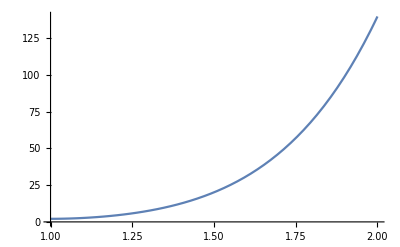

```mathematica
Plot[Abs[w],{q,1,2}]
```

```mathematica
v=Simplify[Together[Z[5,Exp[4π ⅈ/10],1]/._γ->1/.ζ[10]:>Exp[2π ⅈ/10]]]
```

-((8 (-1)^(1/5) (1-(-1)^(1/5)+(-1)^(2/5)-(-1)^(3/5)+(-1)^(4/5)) (-1+q)^10 (1+q)^8 (1+q^2+q^4+q^6+q^8+q^10)^10 (1+q^2+q^4+q^6+q^8+q^10+q^12+q^14+q^16+q^18+q^20)^4)/(5 q^11 (1+(-1)^(3/5) q+q^2+(-1)^(3/5) q^3+q^4+(-1)^(3/5) q^5+q^6+(-1)^(3/5) q^7+q^8+(-1)^(3/5) q^9+q^10+(-1)^(2/5) (-1+(-1)^(1/5)) q^11+q^12+(-1)^(3/5) q^13+q^14+(-1)^(3/5) q^15+q^16+(-1)^(3/5) q^17+q^18+(-1)^(3/5) q^19+q^20+(-1)^(3/5) q^21+q^22) (1+(-1)^(4/5) q+q^2+(-1)^(4/5) q^3+q^4+(-1)^(4/5) q^5+q^6+(-1)^(4/5) q^7+q^8+(-1)^(4/5) q^9+q^10+(-1)^(1/5) (-1+(-1)^(3/5)) q^11+q^12+(-1)^(4/5) q^13+q^14+(-1)^(4/5) q^15+q^16+(-1)^(4/5) q^17+q^18+(-1)^(4/5) q^19+q^20+(-1)^(4/5) q^21+q^22) ((-1)^(1/5)+q+(-1)^(1/5) q^2+q^3+(-1)^(1/5) q^4+q^5+(-1)^(1/5) q^6+q^7+(-1)^(1/5) q^8+q^9+(-1)^(1/5) q^10+(1+(-1)^(2/5)) q^11+(-1)^(1/5) q^12+q^13+(-1)^(1/5) q^14+q^15+(-1)^(1/5) q^16+q^17+(-1)^(1/5) q^18+q^19+(-1)^(1/5) q^20+q^21+(-1)^(1/5) q^22) ((-1)^(1/5)-(-1)^(2/5) q+(-1)^(1/5) q^2-(-1)^(2/5) q^3+(-1)^(1/5) q^4-(-1)^(2/5) q^5+(-1)^(1/5) q^6-(-1)^(2/5) q^7+(-1)^(1/5) q^8-(-1)^(2/5) q^9+(-1)^(1/5) q^10-(1+(-1)^(2/5)) q^11+(-1)^(1/5) q^12-(-1)^(2/5) q^13+(-1)^(1/5) q^14-(-1)^(2/5) q^15+(-1)^(1/5) q^16-(-1)^(2/5) q^17+(-1)^(1/5) q^18-(-1)^(2/5) q^19+(-1)^(1/5) q^20-(-1)^(2/5) q^21+(-1)^(1/5) q^22) ((-1)^(1/5)+(-1)^(2/5) q+(-1)^(1/5) q^2+(-1)^(2/5) q^3+(-1)^(1/5) q^4+(-1)^(2/5) q^5+(-1)^(1/5) q^6+(-1)^(2/5) q^7+(-1)^(1/5) q^8+(-1)^(2/5) q^9+(-1)^(1/5) q^10+(1+(-1)^(2/5)) q^11+(-1)^(1/5) q^12+(-1)^(2/5) q^13+(-1)^(1/5) q^14+(-1)^(2/5) q^15+(-1)^(1/5) q^16+(-1)^(2/5) q^17+(-1)^(1/5) q^18+(-1)^(2/5) q^19+(-1)^(1/5) q^20+(-1)^(2/5) q^21+(-1)^(1/5) q^22) ((-1)^(2/5)+q+(-1)^(2/5) q^2+q^3+(-1)^(2/5) q^4+q^5+(-1)^(2/5) q^6+q^7+(-1)^(2/5) q^8+q^9+(-1)^(2/5) q^10+(1+(-1)^(4/5)) q^11+(-1)^(2/5) q^12+q^13+(-1)^(2/5) q^14+q^15+(-1)^(2/5) q^16+q^17+(-1)^(2/5) q^18+q^19+(-1)^(2/5) q^20+q^21+(-1)^(2/5) q^22) ((-1)^(2/5)-(-1)^(4/5) q+(-1)^(2/5) q^2-(-1)^(4/5) q^3+(-1)^(2/5) q^4-(-1)^(4/5) q^5+(-1)^(2/5) q^6-(-1)^(4/5) q^7+(-1)^(2/5) q^8-(-1)^(4/5) q^9+(-1)^(2/5) q^10-(1+(-1)^(4/5)) q^11+(-1)^(2/5) q^12-(-1)^(4/5) q^13+(-1)^(2/5) q^14-(-1)^(4/5) q^15+(-1)^(2/5) q^16-(-1)^(4/5) q^17+(-1)^(2/5) q^18-(-1)^(4/5) q^19+(-1)^(2/5) q^20-(-1)^(4/5) q^21+(-1)^(2/5) q^22) ((-1)^(2/5)+(-1)^(4/5) q+(-1)^(2/5) q^2+(-1)^(4/5) q^3+(-1)^(2/5) q^4+(-1)^(4/5) q^5+(-1)^(2/5) q^6+(-1)^(4/5) q^7+(-1)^(2/5) q^8+(-1)^(4/5) q^9+(-1)^(2/5) q^10+(1+(-1)^(4/5)) q^11+(-1)^(2/5) q^12+(-1)^(4/5) q^13+(-1)^(2/5) q^14+(-1)^(4/5) q^15+(-1)^(2/5) q^16+(-1)^(4/5) q^17+(-1)^(2/5) q^18+(-1)^(4/5) q^19+(-1)^(2/5) q^20+(-1)^(4/5) q^21+(-1)^(2/5) q^22)))

Contrary to appearances, this is just zero :

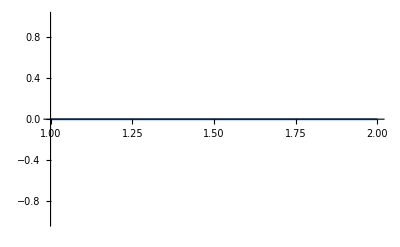

```mathematica
Plot[Abs[v],{q,1,2}]
```